```mathematica
x[n_, m_] := Sqrt[(n+m+1)]/2 /; Abs[n-m] == 1
x[n_, m_] := 0 /; Abs[n-m] != 1
```

```mathematica
p[n_, m_] := I Sqrt[(n+m+1)]/2 /; n - m == 1
p[n_, m_] := -I Sqrt[(n+m+1)]/2 /; n - m == -1
p[n_, m_] := 0 /; Abs[n-m] != 1
```

```mathematica
x[basissize_] := Table[
x[n, m], 
{n, 0, basissize-1}, 
{m, 0, basissize-1} 
]
```

```mathematica
p[basissize_] := Table[
p[n,  m],  
{n, 0, basissize - 1}, 
{m, 0, basissize - 1} 
]
```

```mathematica
h0[basissize_] := DiagonalMatrix [ 
Table[n+1/2, 
{n, 0, basissize-1} 
]
 ]
```

```mathematica
h[basissize_, λ_] := h0[basissize] -x[basissize].x[basissize]/2+ λ x[basissize] . x[basissize] . x[basissize] . x[basissize]. x[basissize] . x[basissize]
```

```mathematica
evals[basissize_, λ_] := Sort [ Eigenvalues [ N[ h[basissize,  λ] ] ] ]
```

```mathematica
e = evals[100, 1/6]
```

{0.434931,1.64831,3.44703,5.67414,8.2496,11.1315,14.2899,17.7024,21.3511,25.2217,29.3021,33.5818,38.0521,42.7051,47.534,52.5331,57.698,63.0187,68.4646,74.0351,79.9616,86.4038,91.2858,95.3769,116.111,116.47,160.191,160.318,227.04,227.117,323.486,323.542,458.707,458.752,644.309,644.346,894.653,894.685,1227.3,1227.33,1663.56,1663.58,2229.06,2229.08,2954.56,2954.58,3876.7,3876.72,5039.07,5039.09,6493.29,6493.31,8300.43,8300.44,10532.6,10532.6,13274.7,13274.7,16627.1,16627.1,20708.1,20708.1,25657.1,25657.1,31639.3,31639.3,38850.3,38850.3,47522.8,47522.8,57934.4,57934.4,70418.4,70418.4,85377.4,85377.4,103301.,103301.,124792.,124792.,150599.,150599.,181666.,181666.,219209.,219209.,264825.,264825.,320684.,320684.,389849.,389849.,476909.,476909.,589348.,589348.,741229.,741229.,967699.,967699.}

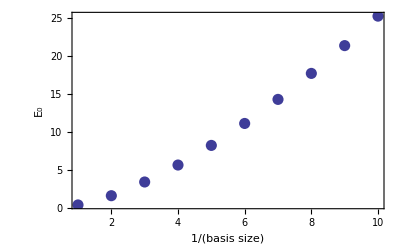

```mathematica
ListPlot[
{
Table[
{b,e[[b]]}, 
{b, 1, 10}]
}, 
Frame -> True, 
Axes -> False, 
PlotStyle -> {PointSize[0.02], Hue[0]}, 
PlotRange -> All, 
FrameLabel -> {"1/(basis size)", "E_0"} 
]
```

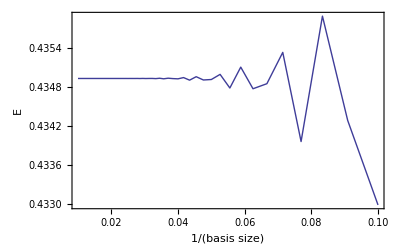

```mathematica
ListPlot[
{
Table[
{1/basissize, evals[basissize, 1/6][[1]]}, 
{basissize, 10, 100}]
}, 
Frame -> True, 
Axes -> False, 
Joined->True,
PlotStyle -> {PointSize[0.02], Hue[0]}, 
PlotRange -> All, 
FrameLabel -> {"1/(basis size)", "E"} 
]
```